### Initialization

```mathematica
SetDirectory[NotebookDirectory[]];
ULISTparton={"u","d","s","c","b",
"g","ubar","dbar","sbar","cbar","bbar"};
ULISTnumparton=
{{1,"u"},{2,"d"},{3,"s"},{4,"c"},{5,"b"},
{0,"g"},
{-1,"ubar"},{-2,"dbar"},{-3,"sbar"},{-4,"cbar"},{-5,"bbar"}};
USetMMApdf::usage="return function head f";
USetMMApdf[XQpdftable_List]:=With[{pdf={#[[1;;2]],#[[3]]}&/@XQpdftable},Interpolation[pdf]]
USetMMApdf[errorInput___]:=(Print["check input List!---&USetMMApdf"];Abort[])
PDFparton[partonname_String,x_,Q_]:=If[StringCases[partonname,ULISTexistparton]≠{},USetMMApdf[ULISTpdf[partonname]][x,Q],Print["check input parton name!---&PDFparton"];Abort[]]
PDFparton[partonnumber_Integer,x_,Q_]:=Which[
partonnumber==1,PDFparton["u",x,Q],
partonnumber==2,PDFparton["d",x,Q],
partonnumber==3,PDFparton["s",x,Q],
partonnumber==4,PDFparton["c",x,Q],
partonnumber==5,PDFparton["b",x,Q],
partonnumber==0,PDFparton["g",x,Q],
partonnumber==-1,PDFparton["ubar",x,Q],
partonnumber==-2,PDFparton["dbar",x,Q],
partonnumber==-3,PDFparton["sbar",x,Q],
partonnumber==-4,PDFparton["cbar",x,Q],
partonnumber==-5,PDFparton["bbar",x,Q],
True,(Print["check input parton number!---&PDFparton"];Abort[])]
PDFparton[errorInput___]:=(Print["check input parameters!---&PDFparton"];Abort[])
Grid@ULISTnumparton
```

1 | u
2 | d
3 | s
4 | c
5 | b
0 | g
-1 | ubar
-2 | dbar
-3 | sbar
-4 | cbar
-5 | bbar

### Import existing parton distribution functions

```mathematica
ULISTpdf;
Do[If[TrueQ[StringCases[fname="pdf_"<>i<>".txt",FileNames[]]≠{}],ULISTpdf[i]=Import[fname,"Data"]],{i,ULISTparton}]
ULISTexistparton=DownValues[ULISTpdf][[All,1]][[All,1,1]]
```

{b,bbar,c,cbar,d,dbar,g,s,sbar,u,ubar}

### Convert PDFs table into interpolation functions

```mathematica
Table[{i,PDFparton[i,x,Q]},{i,ULISTexistparton}]
```

{{b,InterpolatingFunction[…][x,Q]},{bbar,InterpolatingFunction[…][x,Q]},{c,InterpolatingFunction[…][x,Q]},{cbar,InterpolatingFunction[…][x,Q]},{d,InterpolatingFunction[…][x,Q]},{dbar,InterpolatingFunction[…][x,Q]},{g,InterpolatingFunction[…][x,Q]},{s,InterpolatingFunction[…][x,Q]},{sbar,InterpolatingFunction[…][x,Q]},{u,InterpolatingFunction[…][x,Q]},{ubar,InterpolatingFunction[…][x,Q]}}

### Some graphics show

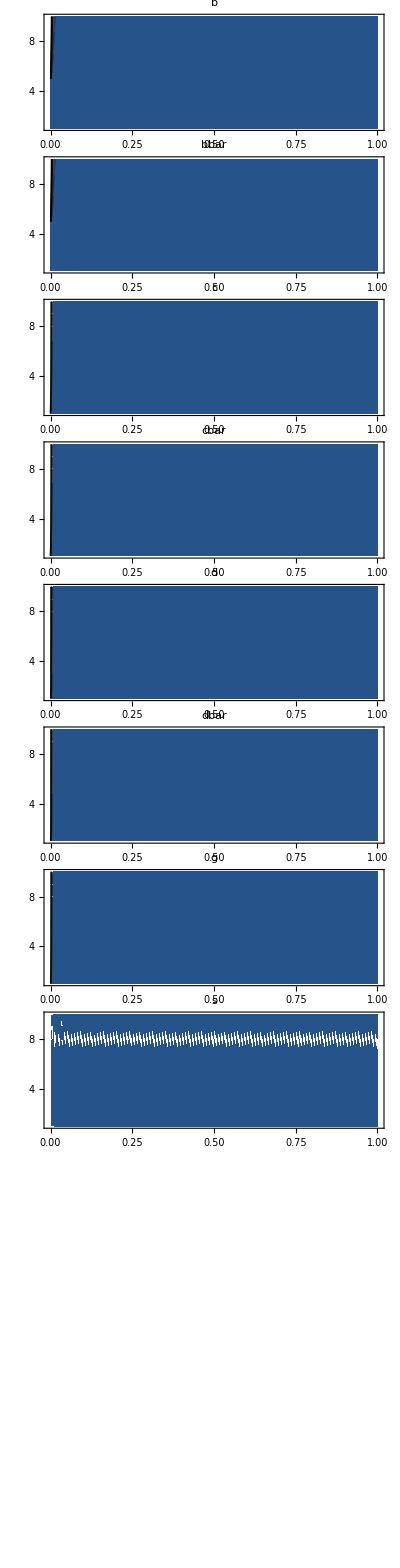

```mathematica
ListContourPlot[ULISTpdf[#],ImageSize->Medium,PlotLabel->#]&/@ULISTexistparton//Column
```

```mathematica
Plot3D[PDFparton["u",x,Q],{x,0.01,1},{Q,1,100},PlotPoints->10]
```

-Graphics3D-